# Scaffold protein titration motif

## The model description

This particular motif describe one phosphorylation-desphosphorylation cycle (can be generalized to any futile cycles) with both kinase (K) and phosphatase (P) can be titrated by a scaffold protein (T).

K + S ⇌ KS → K + S_p
P + S_p ⇌ PS_p → P + S
T + K ⇌ TK
T + P ⇌ TP

The above reactions show a simple system that composed of one scaffold protein, one kinase, one phosphatase and one substrate. Here we try to descibe this simple system with differential equation following the mass action kinetics.

ⅆ[K]/ⅆt=-k[1][K][S]+k[2][KS]+k[3][KS]-k[7][T][K]+k[8][TK],
ⅆ[P]/ⅆt=-k[4][P][S_p]+k[5][PS_p]+k[6][PS_p]-k[9][T][P]+k[10][TP],
ⅆ[S]/ⅆt=-k[1][K][S]+k[2][KS]+k[6][PS_p],
ⅆ[S_p]/ⅆt=-k[4][P][S_p]+k[3][KS]+k[5][PS_p],
ⅆ[KS]/ⅆt=k[1][K][S]-k[2][KS]-k[3][KS],
ⅆ[PS_p]/ⅆt=k[4][P][S_p]-k[5][PS_p]-k[6][PS_p],
ⅆ[T]/ⅆt=-k[7][T][K]+k[8][TK]-k[9][T][P]+k[10][TP],
ⅆ[TK]/ⅆt=k[7][T][K]-k[8][TK],
ⅆ[TP]/ⅆt=k[9][T][P]-k[10][TP].

And the system need to follow these conservation equations:

[K]+[KS]+[TK]=[K_tot],
[P]+[PS_p]+[TP]=[P_tot],
[S]+[S_p]+[KS]+[PS_p]=[S_tot],
[T]+[TK]+[TP]=[T_tot].

In the following setion, we will solve the differential equations to understand the dynamics and behaviour of such system.

## Understanding the dynamics of the simple system with input pertubations (numerical study)

Since, it is a bit difficult to solve the differential equations analytically. Here we try to study them numerically. By defining two different way to characterising the dynamics with scoring their tempral dynamics when presented with input signal perturbation (the changing of [T]). The quantification can be derived from the actually fitness funcitons for ultrasensitive response and adaptive response. Then we save all the parameter sets as well as their score on ultrasensitivity and adaptation.

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];

des={-k1[t]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k1[t]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k1[t]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*^-3};(*init={tot[1],tot[2],tot[3],0.00001,0.00001,0.00001,totT,0.00001,0.00001};*)
```

```mathematica
AbsoluteTiming[
totK=1;totP=1;totS=1;
stepNum=6;
sampleSize=10000;

pars={};
vars=Array[x,9];AppendTo[vars,k1];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
For[num=1,num≤sampleSize,num++,
Block[{k,T,ssthreshold},k[n_]:=k[n]=10^(RandomReal[]*6-3);
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=2.*10^(RandomReal[]*4-3);

Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k1[t]->10*k1[t]}]]},vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[5]]-x4[[3]])]/totS)*Min[((Abs[(x4[[5]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[5]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[5]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*Min[(0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.0001]),1.0])];
];
ad=(ad/0.0001)^(1/(stepNum));

ks=Array[k,10];
AppendTo[pars,Join[ks,{totT,totK,totP,totS,us,ad,num,(ks[[2]]+ks[[3]])/ks[[1]],(ks[[5]]+ks[[6]])/ks[[4]],ks[[8]]/ks[[7]],ks[[10]]/ks[[9]]}]];
];
];
];
];
]

(*Plot@@{{{(x[7][t]+x[8][t]+x[9][t]),x[4][t]}/.sol},Flatten@{t,x[1]["Domain"]/.sol},PlotLegends->{"T_tot","S_p"}}
ListPlot[Transpose@{xT,x4},PlotRange->{0,10}]*)
(*Print[pars];*)
transPars=Transpose[pars];
Export["unsaturationSampling.csv",transPars];
(*Export["unsaturationSampling.csv",transPars];*)
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 864.156 and t = 864.157.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 7377.69 and t = 7377.7.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 5645.8 and t = 5645.8.

General::stop: Further output of NDSolve :: evcvmit will be suppressed during this calculation.

NDSolve::ndcf: Repeated convergence test failure at t == 1.98139; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at t == 0.735788; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at t == 0.0334807; unable to continue.

General::stop: Further output of NDSolve :: ndcf will be suppressed during this calculation.

{1920.32,Null}

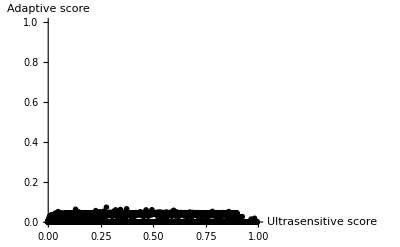

```mathematica
ListPlot[Transpose[{transPars[[15]],transPars[[16]]}],PlotRange->{{0,1},{0,1}},AxesLabel->{"Ultrasensitive score","Adaptive score"},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome"]
```

```mathematica
maxAndIndex[a_]:={#,First@SparseArray[UnitStep[a-#]]["AdjacencyLists"]}&@Max@a
```

```mathematica
paretoIndex=maxAndIndex[transPars[[15]]*transPars[[16]]]//Last
```

5887

```mathematica
transPars[[15]][[paretoIndex]]
```

0.858603

```mathematica
transPars[[16]][[paretoIndex]]
```

0.052417

```mathematica
maxAndIndex[transPars[[15]]]
```

{0.993317,2985}

```mathematica
maxAndIndex[transPars[[16]]]
```

{0.0739352,1405}

```mathematica
usIndex=maxAndIndex[transPars[[15]]]//Last;
adIndex=maxAndIndex[transPars[[16]]]//Last;
paretoIndex=maxAndIndex[transPars[[15]]*transPars[[16]]]//Last
```

5887

```mathematica
pars[[paretoIndex]]
```

{99.5747,0.491439,184.792,328.505,0.00290774,3.12401,0.323566,0.0525213,24.5279,0.00202338,1.16155,1,1,1,0.858603,0.052417,5963,1.86075,0.00951864,0.16232,0.0000824932}

```mathematica
pars[[usIndex]]
```

{4.9608,57.6549,0.0977202,0.00697966,45.4625,0.0193225,0.153842,0.00159569,527.958,0.0551779,2.28487,1,1,1,0.993317,0.,3017,11.6418,6516.34,0.0103722,0.000104512}

```mathematica
pars[[adIndex]]
```

{0.0753899,216.873,62.9984,23.7527,0.00237521,0.026067,0.0157748,548.002,0.00466752,0.00400988,5.39204,1,1,1,0.27698,0.0739352,1426,3712.32,0.00119743,34739.1,0.859103}

{hillK→0.152095,n→4.29876}

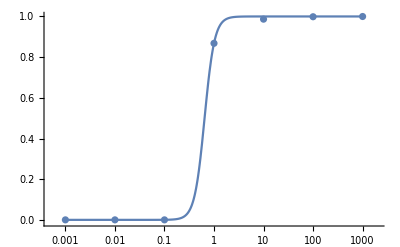

```mathematica
maxAndIndex[a_]:={#,First@SparseArray[UnitStep[a-#]]["AdjacencyLists"]}&@Max@a
usIndex=maxAndIndex[transPars[[15]]]//Last;
adIndex=maxAndIndex[transPars[[16]]]//Last;
stepNum=6;
maxPars=Solve[Array[k,10]==pars[[usIndex]][[Range[10]]]];totT=pars[[usIndex]][[11]];
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *)
{sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[(Norm[df]<ssthreshold),{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k1[t]->10*k1[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol]/totS;k1t=Evaluate[(k1[ts-0.001])/.sol];
];
fittedHill=FindFit[Transpose@{k1t,x4},x^n/(hillK+x^n),{hillK,n},x]
Show[LogLinearPlot[x^n/(hillK+x^n)/.fittedHill,{x,10^-3,10^3},PlotRange->{-0.01,1}],ListLogLinearPlot[Transpose@{k1t,x4}]]
```

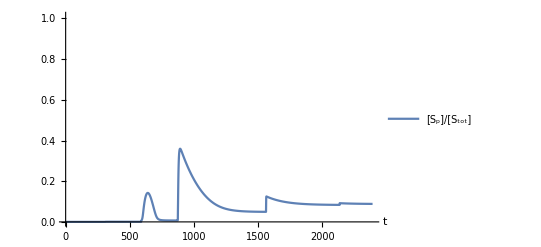

```mathematica
maxPars=Solve[Array[k,10]==pars[[adIndex]][[Range[10]]]];totT=pars[[adIndex]][[11]];
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k1[t]->10*k1[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k1t=Evaluate[(k1[ts-0.001])/.sol];
];
Plot@@{{{x[4][t]/totS}/.sol},Flatten@{t,0,ts[[stepNum]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.85,0.85}],PlotRange->{0,1.01},AxesLabel->{"t"}}
```

5.39204

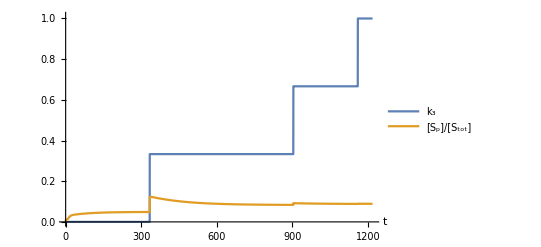

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,1};
stepNum=3;
maxPars=Solve[Array[k,10]==pars[[adIndex]][[Range[10]]]];totT=pars[[adIndex]][[11]]
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k1[t]->10*k1[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k1t=Evaluate[(k1[ts-0.001])/.sol];
];
Plot@@{{{Log10[k1[t]/1]/3,x[4][t]/totS}/.sol},Flatten@{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"k_3","[S_p]/[S_tot]"},{0.85,0.25}],PlotRange->{0,1.01},AxesLabel->{"t"}}
```